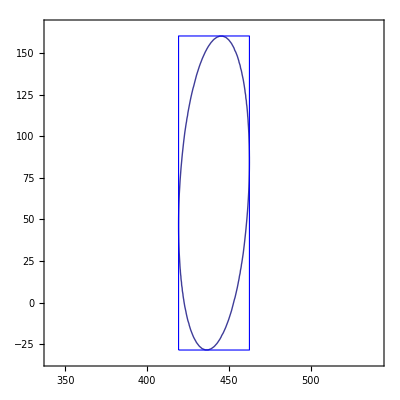

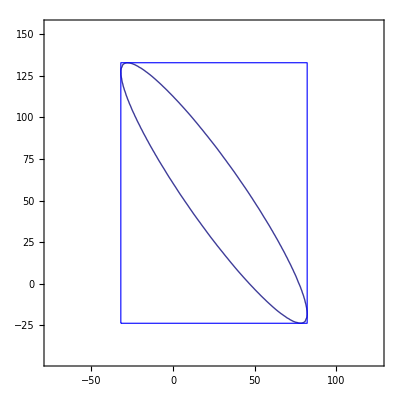

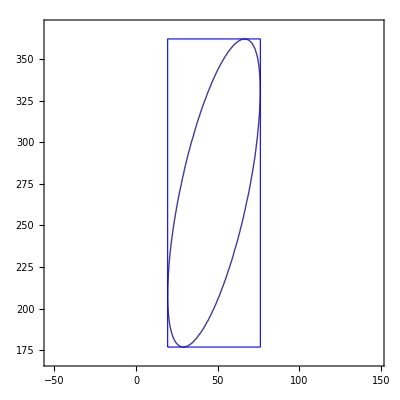

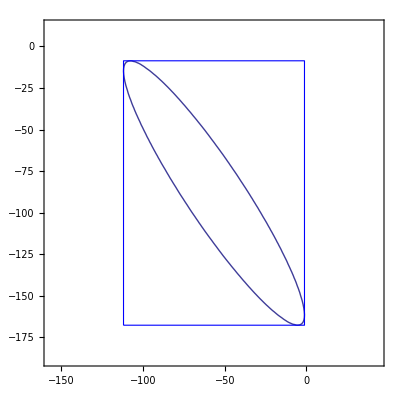

44.0276

86.266

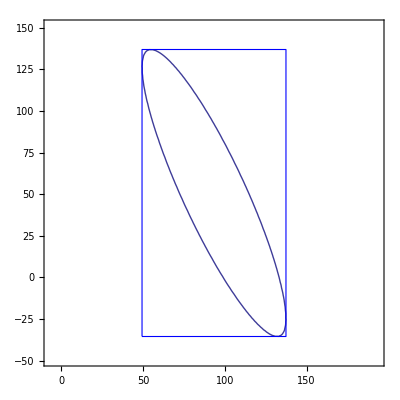

```mathematica
invsigmadl = 1/(63^2);
invsigmaz = 1/(10^2);
(*
angle = 0.20029;
y0 = 269.498;
z0 = 47.7439;

angle = 0.0470448;
y0 = 65.8442;
z0 = 440.8988;

angle = -0.594145;
y0 = 54.5915;
z0 = 25.1197;

*)

angle = 0.0470448;
y0 = 65.8442;
z0 = 440.8988;


a=(((4.0)/(Cos[angle]^ 2))*invsigmadl)+((2*(Tan[angle]^2)*invsigmaz));
b=-4*Tan[angle]*invsigmaz;
c=2*invsigmaz;
b2=(b/2)*(b/2);
bbz=3/Sqrt[c-(b2/a)]
bby=3/Sqrt[a-(b2/c)]


ellipse[y0_,z0_]=Graphics[ContourPlot[(((a*((y0 - dy)*(y0 -dy)))+(b*(y0 -dy)*(z0 -dz))+(c*((z0 -dz)*(z0 -dz)))))==9,{dz,z0-100,z0+100},{dy,y0-100,y0+100}]];

rect[y0_,z0_] = Graphics[{EdgeForm[{Thick,Blue}],FaceForm[],Rectangle[{z0-bbz,y0-bby},{z0+bbz,y0+bby}]},Frame->True];
Show[ellipse[y0,z0],rect[y0,z0]]

angle = -0.594145;
y0 = 54.5915;
z0 = 25.1197;


a=(((4.0)/(Cos[angle]^ 2))*invsigmadl)+((2*(Tan[angle]^2)*invsigmaz));
b=-4*Tan[angle]*invsigmaz;
c=2*invsigmaz;
b2=(b/2)*(b/2);
bbz=3/Sqrt[c-(b2/a)]
bby=3/Sqrt[a-(b2/c)]


ellipse[y0_,z0_]=Graphics[ContourPlot[(((a*((y0 - dy)*(y0 -dy)))+(b*(y0 -dy)*(z0 -dz))+(c*((z0 -dz)*(z0 -dz)))))==9,{dz,z0-100,z0+100},{dy,y0-100,y0+100}]];

rect[y0_,z0_] = Graphics[{EdgeForm[{Thick,Blue}],FaceForm[],Rectangle[{z0-bbz,y0-bby},{z0+bbz,y0+bby}]},Frame->True];
Show[ellipse[y0,z0],rect[y0,z0]]

angle = 0.20029;
y0 = 269.498;
z0 = 47.7439;

a=(((4.0)/(Cos[angle]^ 2))*invsigmadl)+((2*(Tan[angle]^2)*invsigmaz));
b=-4*Tan[angle]*invsigmaz;
c=2*invsigmaz;
b2=(b/2)*(b/2);
bbz=3/Sqrt[c-(b2/a)]
bby=3/Sqrt[a-(b2/c)]


ellipse[y0_,z0_]=Graphics[ContourPlot[(((a*((y0 - dy)*(y0 -dy)))+(b*(y0 -dy)*(z0 -dz))+(c*((z0 -dz)*(z0 -dz)))))==9,{dz,z0-100,z0+100},{dy,y0-100,y0+100}]];

rect[y0_,z0_] = Graphics[{EdgeForm[{Thick,Blue}],FaceForm[],Rectangle[{z0-bbz,y0-bby},{z0+bbz,y0+bby}]},Frame->True];
Show[ellipse[y0,z0],rect[y0,z0]]

angle = -0.571667;
y0 = -88.1376;
z0 = -56.5727;

a=(((4.0)/(Cos[angle]^ 2))*invsigmadl)+((2*(Tan[angle]^2)*invsigmaz));
b=-4*Tan[angle]*invsigmaz;
c=2*invsigmaz;
b2=(b/2)*(b/2);
bbz=3/Sqrt[c-(b2/a)]
bby=3/Sqrt[a-(b2/c)]


ellipse[y0_,z0_]=Graphics[ContourPlot[(((a*((y0 - dy)*(y0 -dy)))+(b*(y0 -dy)*(z0 -dz))+(c*((z0 -dz)*(z0 -dz)))))==9,{dz,z0-100,z0+100},{dy,y0-100,y0+100}]];

rect[y0_,z0_] = Graphics[{EdgeForm[{Thick,Blue}],FaceForm[],Rectangle[{z0-bbz,y0-bby},{z0+bbz,y0+bby}]},Frame->True];
Show[ellipse[y0,z0],rect[y0,z0]]

angle = -0.420542;
y0 = 50.7004;
z0 = 93.3057;

a=(((4.0)/(Cos[angle]^ 2))*invsigmadl)+((2*(Tan[angle]^2)*invsigmaz));
b=-4*Tan[angle]*invsigmaz;
c=2*invsigmaz;
b2=(b/2)*(b/2);

bbz=3/Sqrt[c-(b2/a)]
bby=3/Sqrt[a-(b2/c)]


ellipse[y0_,z0_]=Graphics[ContourPlot[(((a*((y0 - dy)*(y0 -dy)))+(b*(y0 -dy)*(z0 -dz))+(c*((z0 -dz)*(z0 -dz)))))==9,{dz,z0-100,z0+100},{dy,y0-100,y0+100}]];

rect[y0_,z0_] = Graphics[{EdgeForm[{Thick,Blue}],FaceForm[],Rectangle[{z0-bbz,y0-bby},{z0+bbz,y0+bby}]},Frame->True];
Show[ellipse[y0,z0],rect[y0,z0]]
```